```mathematica
$Assumptions-> t∈Reals&&Im[t]==0&&l∈Integers&&Im[l]==0;
```

```mathematica
F[t_]:= Sign[Cos[t]];
```

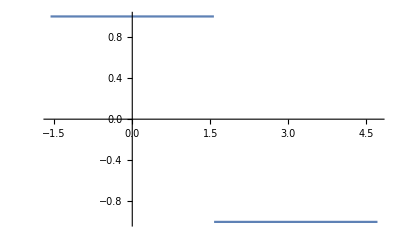

```mathematica
Plot[F[t],{t,-Pi/2,3Pi/2}]
```

```mathematica
1/(2Pi)Integrate[Exp[I l t]F[t],{t,-Pi/2,3Pi/2}]//FullSimplify
```

-((-1+ⅇ^(ⅈ l π)) Sin[(l π)/2])/(l π)

```mathematica
c[l_]:=-((-1+ⅇ^(ⅈ l π)) Sin[(l π)/2])/(l π);
```

```mathematica
Sum2 = Sum[c[l]c[-l]/(l^2),{l,1,500}];
kappa2[t_]:= -(Sum[c[n]/(n^2)Exp[-I n t],{n,1,200}]+Sum[c[-n]/(n^2)Exp[I n t],{n,1,200}]);
```

```mathematica
Sum2//N
```

0.411234

```mathematica
Pi^2/24//N
```

0.411234

```mathematica
kappa2[0]//N
```

-1.2337

```mathematica
-Pi^2/8//N
```

-1.2337

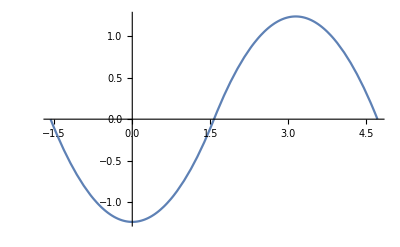

```mathematica
Plot[kappa2[t]//N,{t,-Pi/2,3Pi/2}]
```